```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->NotebookDirectory[]]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,0->3],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"DF2"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"DF2"}]];
```

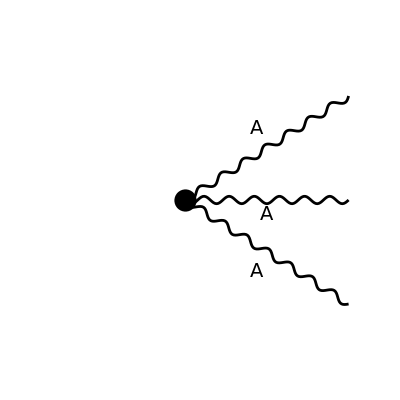

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3},LoopMomenta->{},ChangeDimension->4,List->False];
```

```mathematica
(*FCClearScalarProducts[];
SetMandelstam[x,{ p1 , p2, p3} ,{ 0 , 0 , 0} ];*)
```

```mathematica
amp[1]=amp[0] // Contract // SUNSimplify;
```

```mathematica
amp[2] = amp[1] // ExpandScalarProduct;
```

```mathematica
amp[3] =FeynAmpDenominatorExplicit[amp[2]] ;
```

```mathematica
amp[4]=FeynCalcExternal[amp[3]];
```

```mathematica
amp[5]=amp[4]/.SP[p3,p3]->0/.SP[p1,p1]->0/.SP[p2,p2]->0;
```

```mathematica
amp[6]=amp[5]/.SP[x_,Polarization[x_,y_]]->0;
```

```mathematica
amp[6]/.p3->-p2-p1//ExpandScalarProduct//FeynCalcExternal//Simplify
```

-g (2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[-p1-p2,-ⅈ]]-2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[-p1-p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p2] SP[Polarization[p1,-ⅈ],Polarization[-p1-p2,-ⅈ]]-m^2 SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[-p1-p2,-ⅈ]]+2 SP[p1,p2] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[-p1-p2,-ⅈ]]-m^2 SP[p2,Polarization[-p1-p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,p1] SP[p2,Polarization[-p1-p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,p2] SP[p2,Polarization[-p1-p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[-p1-p2,-ⅈ]] (-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]]+(m^2+2 SP[p1,p2]+2 SP[p2,p2]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]])+2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[-p1-p2,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,p1] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[-p1-p2,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p1,-ⅈ]] (2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[-p1-p2,-ⅈ]]+(m^2-2 SP[p1,p2]) SP[Polarization[-p1-p2,-ⅈ],Polarization[p2,-ⅈ]])) SUNF[a1,a2,a3]

```mathematica
%/.m->0
```

-g (-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]) SUNF[a1,a2,a3]

```mathematica
diags2=InsertFields[CreateTopologies[0,0->4],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}],V[1,{a4}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"DF2"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"DF2"}]];
```

```mathematica
amp2[0]=FCFAConvert[CreateFeynAmp[diags2, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3,p4},LoopMomenta->{},ChangeDimension->4,List->False]//Contract // SUNSimplify//FeynAmpDenominatorExplicit//ExpandScalarProduct//FeynCalcExternal
```

```mathematica
%/.SP[x_,x_]->0/.SP[x_,Polarization[x_,y_]]->0/.SP[Polarization[x_,y_],Polarization[x_,y_]]->0
```

ⅈ g^2 ((c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]])/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+(1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+(1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+(1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]-ⅈ g^2 (4 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-4 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV[sun6891]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV[sun6891]]]+(-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (SP[p2,p3]+SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p2] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+(-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (SP[p2,p3]+SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p2] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+(-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p4]) (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p4,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (SP[p2,p3]+SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p3,-ⅈ]]+SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])ⅈ g^2 (SP[p1,p2]+SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p4] (SP[p2,p3]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p3,p4]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] SP[p4,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p3,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]]) (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])2 ⅈ g^2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p2] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p2,p4])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p2,p4])4 ⅈ g^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p4]) (m^2-2 SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))2 ⅈ g^2 SP[p1,p3] (m^2-2 SP[p2,p4]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p4] (-m^2+2 SP[p2,p4]))ⅈ g^2 m^2 (m^2-2 SP[p2,p4]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]-ⅈ g^2 (4 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-4 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[FCGV[sun6891]]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[FCGV[sun6891]]]+(-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p1,p3]-SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p1,p3]+SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p2,p3]-SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p2,p3]+SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+(-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polariz

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a3],x_]->0
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[FCGV[x_]]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[FCGV[x_]]]->1
```

```mathematica
%/.SUNF[y_,z_,ExplicitSUNIndex[2]] ->0
```

```mathematica
%/.SUNF[y_,z_,ExplicitSUNIndex[3]] ->0
```

-ⅈ g^2 (2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+4 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-4 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+ⅈ g^2 ((c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]])/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+(1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]-ⅈ g^2 (4 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-4 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV[sun6891]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV[sun6891]]]+(-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p1,p3]-SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p1,p3]+SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p2,p3]-SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p2,p3]+SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV["sun6891"]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV["sun6891"]]]->-1
```

ⅈ g^2 (4 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-4 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-ⅈ g^2 (2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+4 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-4 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+ⅈ g^2 ((c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]])/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+(1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+(-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p1,p3]-SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p1,p3]+SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p2,p3]-SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p2,p3]+SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]->-1
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]->1
```

-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p3,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p4,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,Polarization[p3,-ⅈ]] (m^2-2 SP[p2,p3]) (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,p4]+SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p3] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,p3] (SP[p2,Polarization[p4,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) SP[p3,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p1,p2]-SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p1,p2]+SP[p1,p3]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])ⅈ g^2 (SP[p1,p2]+SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p3] (SP[p2,p4]+SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p4,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,Polarization[p4,-ⅈ]] (-SP[p2,p4]-SP[p3,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] SP[p3,Polarization[p1,-ⅈ]] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p4] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,Polarization[p4,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])2 ⅈ g^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p2] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 SP[p1,p3] (-SP[p2,p4]-SP[p3,p4]) SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(-m^2+2 SP[p2,p3])ⅈ g^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-m^2 SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])4 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] (m^2-2 SP[p3,p4]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))2 ⅈ g^2 SP[p1,p2] (m^2-2 SP[p3,p4]) (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (m^2-2 SP[p3,p4]) (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 SP[p1,p4] (m^2-2 SP[p2,p3]) (-SP[p2,Polarization[p1,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) (SP[p2,Polarization[p1,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]]) SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p2,p3]+SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p2,p3])4 ⅈ g^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))ⅈ g^2 m^2 (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(SP[p2,p3] (-m^2+2 SP[p2,p3]))2 ⅈ g^2 (-SP[p1,p2]-SP[p1,p3]) (m^2-2 SP[p2,p3]) SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,p4] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (SP[p3,Polarization[p2,-ⅈ]]+SP[p4,Polarization[p2,-ⅈ]]) SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p1,p3]-SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p1,p3]+SP[p1,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] (SP[p2,p3]+SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p1,p3]+SP[p1,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (-SP[p2,p3]-SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(-m^2+2 SP[p3,p4])ⅈ g^2 (SP[p2,p3]+SP[p2,p4]) SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p3,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p4] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,Polarization[p2,-ⅈ]] (-SP[p2,p3]-SP[p2,p4]) SP[p4,Polarization[p1,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p2,-ⅈ]] (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] SP[p2,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] SP[p4,Polarization[p1,-ⅈ]] (-SP[p3,Polarization[p2,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]]) (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])2 ⅈ g^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p2] (-SP[p3,Polarization[p1,-ⅈ]]-SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 (SP[p3,Polarization[p1,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]]) SP[p4,Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(-m^2+2 SP[p3,p4])ⅈ g^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p3] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 SP[p1,p4] (-SP[p2,p3]-SP[p2,p4]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 m^2 SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-1/(SP[p3,p4] (-m^2+2 SP[p3,p4]))ⅈ g^2 (-SP[p1,p3]-SP[p1,p4]) SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] (2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+ⅈ g^2 (4 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-4 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])-ⅈ g^2 (2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+4 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-4 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-4 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+4 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+m^2 SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])+ⅈ g^2 (1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]+1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p3,p4] (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p4] (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 SP[p2,p3] (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a1,a4] c[1,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a2,a3] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[1,a3,a2] c[1,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a1,a4] c[2,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a2,a3] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[2,a3,a2] c[2,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a2,a3] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a1,a4] c[3,a3,a2] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a2,a3] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p3]))c[3,a3,a2] c[3,a4,a1] SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a2,a4] c[1,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a1,a3] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[1,a3,a1] c[1,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a2,a4] c[2,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a1,a3] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[2,a3,a1] c[2,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a2,a4] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a2,a4] c[3,a3,a1] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a1,a3] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p2,p4]))c[3,a3,a1] c[3,a4,a2] SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a1,a2] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[1,a2,a1] c[1,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a1,a2] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[2,a2,a1] c[2,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a3,a4] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a1,a2] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+1/(2 (-m^2+2 SP[p3,p4]))c[3,a2,a1] c[3,a4,a3] SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]])

```mathematica
%/.c[2,x_,y_]c[2,z_,w_]->0
```

```mathematica
%/.c[3,x_,y_]c[3,z_,w_]->0
```